# Cvičenie 3 - jednorozmerné polia a práca so súbormi

Jednorozmerné pole

### Úloha 1

Dané je jednorozmerné pole a, ktorého prvky sú a={ 10,-2,5,9,10,7,-5,-3,-1,5  }. 

Čo najjednoduchšie zistite:
- počet prvkov poľa a
- siedmy prvok od začiatku poľa a piaty prvok od konca poľa a
- do jednorozmerného poľa b vyberte a zapíšte druhý, tretí a štvrtý prvok poľa a (aspoň tromi spôsobmi)
- miesto (pozíciu), kde sa v poli nachádza prvok 10
- maximálny a minimálny prvok
- súčet všetkých prvkov a aritmetický priemer všetkých prvkov
- počet prvkov z poľa a, ktorých hodnota je menšia ako + 4
- súčet prvkov z poľa a, ktorých hodnota je menšia ako + 4

#### Najskôr zadefinujme pole A

```mathematica
Clear[a]
a={10,-2,5,9,10,7,-5,-3,-1,5}
```

{10,-2,5,9,10,7,-5,-3,-1,5}

#### Môžeme použiť aj plný tvar príkazu (tento spôsob sa používa zriedkavejšie)

```mathematica
Clear[a]
a=List[10,-2,5,9,10,7,-5,-3,-1,5]
```

{10,-2,5,9,10,7,-5,-3,-1,5}

#### Počet prvkov jednorozmerného poľa určíme pomocou príkazu Length[ ]

```mathematica
Length[a]
```

10

#### Siedmy prvok od začiatku poľa A určíme

```mathematica
a[[7]]
```

-5

#### Piaty prvok od konca poľa A určíme

```mathematica
a[[-5]]
```

7

#### Do jednorozmerného poľa b vyberte a zapíšte druhý, tretí a štvrtý prvok poľa a (aspoň tromi spôsobmi)

1. spôsob - naprimitívnejší

```mathematica
b={a[[2]],a[[3]],a[[4]]}
```

{-2,5,9}

2. spôsob

```mathematica
b=a[[2;;4]]
```

{-2,5,9}

3. spôsob

```mathematica
b=Take[a,{2,4}]
```

{-2,5,9}

4. spôsob

```mathematica
b=a[[{2,3,4}]]
```

{-2,5,9}

5. spôsob

```mathematica
b=Part[a,{2,3,4}]
```

{-2,5,9}

#### Miesto (pozíciu), kde sa v poli nachádza prvok 8

```mathematica
Position[a,10]
```

{{1},{5}}

Maximálny a minimálny prvok

```mathematica
Max[a]
```

10

```mathematica
Min[a]
```

-5

#### Súčet všetkých prvkov - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať

1. spôsob

```mathematica
Sum[a[[i]],{i,1, Length[a]}]
```

35

2. spôsob

```mathematica
∑_(i=1)^10 a[[i]]
```

35

3. spôsob

```mathematica
Apply[Plus, a]
```

35

4. spôsob

```mathematica
sucet=0;
Do[sucet=sucet+a[[i]],{i,1,Length[a]}]
sucet
```

35

5. spôsob

```mathematica
Total[a]
```

35

#### Aritmetický priemer všetkých prvkov - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať

1. spôsob

```mathematica
1/Length[a]* Sum[a[[i]],{i,1, Length[a]}]
```

7/2

2. spôsob

```mathematica
1/10∑_(i=1)^10 a[[i]]
```

7/2

3. spôsob

```mathematica
Mean[a]
```

7/2

4. spôsob  - funkcionálne programovanie

```mathematica
1/Length[a]*Apply[Plus,a]
```

7/2

#### Počet prvkov z poľa a, ktorých hodnota je menšia ako + 4 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob - procedurálne programovanie

```mathematica
pocet=0;
Do[
If[a[[i]]<4, pocet=pocet+1],
{i,1,Length[a]}];
pocet
```

4

2. spôsob  - pomocou pure function

```mathematica
b=Select[a,#<4&]
Length[b]
```

{-2,-5,-3,-1}

4

3. spôsob - pomocou predikátových funkcií - toto si ešte porobne budeme vysvetľovať na prednáške

```mathematica
testQ[x_]=If[x<4, True, False];
Map[testQ,a]
```

{False,True,False,False,False,False,True,True,True,False}

```mathematica
Select[a,testQ]
```

{-2,-5,-3,-1}

```mathematica
Select[a,testQ]//Length
```

4

#### Súčet prvkov z poľa a, ktorých hodnota je menšia ako + 4 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob  - procedurálne programovanie

```mathematica
sucet=0;
Do[
If[a[[i]]<4, sucet=sucet+a[[i]]  ],
{i,1,Length[a]}];
sucet
```

-11

2. spôsob - pomocou pure function

```mathematica
b=Select[a,#<4&]
Total[b]
```

{-2,-5,-3,-1}

-11

3. spôsob - pomocou predikátových funkcií

```mathematica
testQ[x_]=If[x<4, True, False];
Select[a,testQ]//Total
```

-11

4. spôsob - pomocou predikátových funkcií a funkcion8lneho programovania

```mathematica
testQ[x_]=If[x<4, True, False];
b=Select[a,testQ]
Apply[Plus, b]
```

{-2,-5,-3,-1}

-11

### Úloha 2

Dané je jednorozmerné pole b, ktorého prvky sú dané predpisom (i^2 - 1)/(i^2+i-7) ak i∈[-5,12], i je typu Integer.  Vytvorte toto pole a nakreslite jeho prvky.
Čo najjednoduchšie zitite:
- maximálny a minimálny prvok
- súčet všetkých prvkov a aritmetický priemer všetkých prvkov
- počet prvkov z poľa b, ktorých hodnota je väčšia ako -0.2 a menšia ako +0.3
- súčet prvkov z poľa b, ktorých hodnota je väčšia ako -0.2 a menšia ako +0.3

```mathematica
Clear[b]
b=Table[(i^2-1)/(i^2+i-7),{i,-5,12}]
```

{24/13,3,-8,-3/5,0,1/7,0,-3,8/5,15/13,24/23,1,48/49,63/65,80/83,99/103,24/25,143/149}

```mathematica
Clear[b]
b=Table[(i^2-1)/(i^2+i-7),{i,-5,12}]//N
```

{1.84615,3.,-8.,-0.6,0.,0.142857,0.,-3.,1.6,1.15385,1.04348,1.,0.979592,0.969231,0.963855,0.961165,0.96,0.959732}

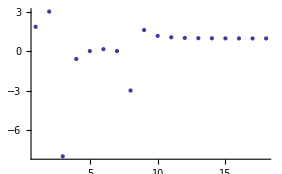

```mathematica
ListPlot[b]
```

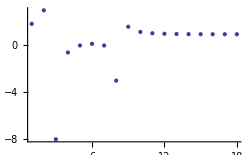

```mathematica
ListPlot[b, PlotRange->All]
```

#### Maximálny a minimálny prvok

```mathematica
Max[b]
```

3.

```mathematica
Min[b]
```

-8.

#### Súčet všetkých prvkov - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať

1. spôsob

```mathematica
Sum[b[[i]],{i,1, Length[b]}]
```

3.97991

2. spôsob

```mathematica
∑_(i=1)^Length[b] b[[i]]
```

3.97991

3. spôsob

```mathematica
Apply[Plus, b]
```

3.97991

4. spôsob

```mathematica
sucet=0;
Do[sucet=sucet+b[[i]],{i,1,Length[b]}]
sucet
```

3.97991

5. spôsob

```mathematica
Total[b]
```

3.97991

#### Aritmetický priemer všetkých prvkov - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať

1. spôsob

```mathematica
1/Length[b]* Sum[b[[i]],{i,1, Length[b]}]
```

0.221106

2. spôsob

```mathematica
Length[b]
```

18

```mathematica
1/Length[b]∑_(i=1)^18 b[[i]]
```

0.221106

3. spôsob

```mathematica
Mean[b]
```

0.221106

4. spôsob

```mathematica
1/Length[b]*Apply[Plus,b]
```

0.221106

#### Počet prvkov z poľa b, ktorých hodnota je väčšia ako -0.2 a menšia alebo rovná ako +0.3 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob - procedurálne programovanie

```mathematica
pocet=0;
Do[
If[-0.2<b[[i]]<=0.3, pocet=pocet+1],
{i,1,Length[b]}];
pocet
```

3

2. spôsob  - pomocou pure function

```mathematica
Select[b,-0.2<#≤0.3&]//N
Length[%]
```

{0.,0.142857,0.}

3

3. spôsob - pomocou predikátových funkcií

```mathematica
testQ[x_]=If[-0.2<x≤0.3, True, False];
Map[testQ,b]
```

{False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Select[b//N,testQ]
```

{0.,0.142857,0.}

```mathematica
Select[b,testQ]//Length
```

3

#### Súčet prvkov z poľa b, ktorých hodnota je väčšia ako -0.2 a menšia alebo rovná ako +0.3 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob  - procedurálne programovanie

```mathematica
sucet=0;
Do[
If[-0.2<b[[i]]≤0.3, sucet=sucet+b[[i]]  ],
{i,1,Length[b]}];
sucet//N
```

0.142857

2. spôsob - pomocou pure function

```mathematica
Select[b,-0.2<#≤0.3&]//N
Total[%]
```

{0.,0.142857,0.}

0.142857

3. spôsob - pomocou predikátových funkcií

```mathematica
testQ[x_]=If[-0.2<x≤0.3, True, False];
Select[b,testQ]//Total//N
```

0.142857

4. spôsob - pomocou predikátových funkcií a funkcion8lneho programovania

```mathematica
testQ[x_]=If[-0.2<x≤0.3, True, False];
b1=Select[b,testQ]//N
Apply[Plus, b1]//N
```

{0.,0.142857,0.}

0.142857

Práca s dátovým súborom

### Úloha 3

V súbore data.txt, ktorý je uložený v AISe sú uložené dáta pochádzajúce z merania.  Načítajte tieto dáta do poľa c a nakreslite jeho prvky.
Čo najjednoduchšie zitite:
- rozsah hodnôt poľa
- počet prvkov z poľa c, ktorých hodnota je väčšia ako -0.47 a menšia ako +0.75
- súčet absolútnych hodnôt prvkov z poľa c, ktorých hodnota je väčšia ako -0.47 a menšia ako +0.75

```mathematica
SetDirectory["c:/Temp/Home"]
```

c:\Temp\Home

```mathematica
Clear[c]
c=ReadList["data.txt"]
```

{1.0319,0.308453,-1.91255,1.11586,1.28502,0.782348,0.0936703,-1.15767,1.74109,0.591556,-0.132294,-1.01518,-1.02891,-0.673562,-1.63703,0.561629,1.37958,1.5688,-0.0248452,-1.9137,0.205027,-0.410374,-0.110496,-1.69508,1.17313,1.28117,-0.197945,-0.810941,1.88811,-1.50117,1.70838,-1.65327,-1.85299,-0.0927311,-0.159321,1.36191,1.17593,-1.41917,-0.522288,-1.19972,1.79635,-0.987968,1.50256,-1.28602,-0.408681,1.42241,-0.386947,-1.59094,0.418191,-1.85877,1.811,1.22,0.530084,1.64241,-1.89739,0.873268,0.383069,-0.264861,0.261936,1.51136,1.20714,-0.845692,-1.21578,0.711077,1.4108,-1.85772,-0.718334,-0.0029049,-0.180522,-1.28013,1.66861,-0.411964,1.40129,-1.42136,1.85761,0.368036,-1.1288,-1.06377,1.755,1.49477,0.488134,1.20109,-0.506935,1.98341,1.28099,0.0467819,-1.29116,-0.727667,1.87019,-0.0954936,1.42717,1.27524,0.0507161,-0.815363,1.75856,-0.312799}

Ak máte problém s načítaním dát zo súboru, skús jednoduchý trik. Použite na na čítanie príkaz ReadList spolu so špecifikáciou očakávaných dát. Veľmi často je totiž problém skrytý práve v tom, ze Mathematica interpretuje číselné dáta ako text.

```mathematica
Clear[c]
c=ReadList["data.txt",Number]
```

{1.0319,0.308453,-1.91255,1.11586,1.28502,0.782348,0.0936703,-1.15767,1.74109,0.591556,-0.132294,-1.01518,-1.02891,-0.673562,-1.63703,0.561629,1.37958,1.5688,-0.0248452,-1.9137,0.205027,-0.410374,-0.110496,-1.69508,1.17313,1.28117,-0.197945,-0.810941,1.88811,-1.50117,1.70838,-1.65327,-1.85299,-0.0927311,-0.159321,1.36191,1.17593,-1.41917,-0.522288,-1.19972,1.79635,-0.987968,1.50256,-1.28602,-0.408681,1.42241,-0.386947,-1.59094,0.418191,-1.85877,1.811,1.22,0.530084,1.64241,-1.89739,0.873268,0.383069,-0.264861,0.261936,1.51136,1.20714,-0.845692,-1.21578,0.711077,1.4108,-1.85772,-0.718334,-0.0029049,-0.180522,-1.28013,1.66861,-0.411964,1.40129,-1.42136,1.85761,0.368036,-1.1288,-1.06377,1.755,1.49477,0.488134,1.20109,-0.506935,1.98341,1.28099,0.0467819,-1.29116,-0.727667,1.87019,-0.0954936,1.42717,1.27524,0.0507161,-0.815363,1.75856,-0.312799}

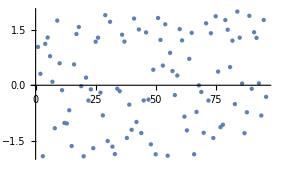

```mathematica
ListPlot[c]
```

Podstatné pre vás je - dostať akýmkoľvek spôsobom dáta do Mathematice  - a potom ich už budeme vedieť spracovať

#### Rozsah, v ktorom sa prvky nachádzajú

```mathematica
Print["prvky poľa ležia v intervale (",Min[c]," , ",Max[c],")"]
```

prvky poľa ležia v intervale (-1.9137 , 1.98341)

#### Počet prvkov z poľa c, ktorých hodnota je väčšia ako -0.47 a menšia ako +0.75 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob - procedurálne programovanie

```mathematica
pocet=0;
Do[
If[-0.47<c[[i]]<0.75, pocet=pocet+1],
{i,1,Length[c]}];
pocet
```

29

2. spôsob  - pomocou pure function

```mathematica
Select[c,-0.47<#<0.75&]
Length[%]
```

{0.308453,0.0936703,0.591556,-0.132294,0.561629,-0.0248452,0.205027,-0.410374,-0.110496,-0.197945,-0.0927311,-0.159321,-0.408681,-0.386947,0.418191,0.530084,0.383069,-0.264861,0.261936,0.711077,-0.0029049,-0.180522,-0.411964,0.368036,0.488134,0.0467819,-0.0954936,0.0507161,-0.312799}

29

3. spôsob - pomocou predikátových funkcií

```mathematica
testQ[x_]=If[-0.47<x<0.75, True, False];
Map[testQ,c]
```

{False,True,False,False,False,False,True,False,False,True,True,False,False,False,False,True,False,False,True,False,True,True,True,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,False,False,False,True,True,True,False,False,False,False,True,False,False,False,True,True,False,False,True,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,True,False,False,True,False,False,True}

```mathematica
Select[c,testQ]
```

{0.308453,0.0936703,0.591556,-0.132294,0.561629,-0.0248452,0.205027,-0.410374,-0.110496,-0.197945,-0.0927311,-0.159321,-0.408681,-0.386947,0.418191,0.530084,0.383069,-0.264861,0.261936,0.711077,-0.0029049,-0.180522,-0.411964,0.368036,0.488134,0.0467819,-0.0954936,0.0507161,-0.312799}

```mathematica
Select[c,testQ]//Length
```

29

#### Súčet absolútnych hodnôt prvkov z poľa c, ktorých hodnota je väčšia ako -0.47 a menšia ako +0.75 - ukážeme si niekoľko spôsobov ako danú úlohu naprogramovať Stačí, ak budete rozumieť a ovládať prvý spôsob, tie ostatné sú pre tých, ktorých to zaujíma viac

1. spôsob  - procedurálne programovanie

```mathematica
sucet=0;
Do[
If[-0.47<c[[i]]<0.75, sucet=sucet+Abs[c[[i]]]  ],
{i,1,Length[c]}];
sucet
```

8.21054

2. spôsob - pomocou pure function

```mathematica
c1=Select[c,-0.47<#<0.75&]
Total[Abs[c1]]
```

{0.308453,0.0936703,0.591556,-0.132294,0.561629,-0.0248452,0.205027,-0.410374,-0.110496,-0.197945,-0.0927311,-0.159321,-0.408681,-0.386947,0.418191,0.530084,0.383069,-0.264861,0.261936,0.711077,-0.0029049,-0.180522,-0.411964,0.368036,0.488134,0.0467819,-0.0954936,0.0507161,-0.312799}

8.21054

3. spôsob - pomocou predikátových funkcií

```mathematica
testQ[x_]=If[-0.47<x<0.75, True, False];
Select[c,testQ]//Abs//Total
```

8.21054

4. spôsob - pomocou predikátových funkcií a funkcion8lneho programovania

```mathematica
testQ[x_]=If[-0.47<x<0.75, True, False];
c1=Select[c,testQ]
Apply[Plus, Abs[c1]]
```

{0.308453,0.0936703,0.591556,-0.132294,0.561629,-0.0248452,0.205027,-0.410374,-0.110496,-0.197945,-0.0927311,-0.159321,-0.408681,-0.386947,0.418191,0.530084,0.383069,-0.264861,0.261936,0.711077,-0.0029049,-0.180522,-0.411964,0.368036,0.488134,0.0467819,-0.0954936,0.0507161,-0.312799}

8.21054

### Úloha 4 - práca s dátovými súbormi v rôznych formátoch

#### Úloha načítajte dáta zo súboru data.txt

```mathematica
SetDirectory["c:/Temp/Home"]
```

c:\Temp\Home

```mathematica
Clear[c]
c=ReadList["data.txt"]
```

{1.0319,0.308453,-1.91255,1.11586,1.28502,0.782348,0.0936703,-1.15767,1.74109,0.591556,-0.132294,-1.01518,-1.02891,-0.673562,-1.63703,0.561629,1.37958,1.5688,-0.0248452,-1.9137,0.205027,-0.410374,-0.110496,-1.69508,1.17313,1.28117,-0.197945,-0.810941,1.88811,-1.50117,1.70838,-1.65327,-1.85299,-0.0927311,-0.159321,1.36191,1.17593,-1.41917,-0.522288,-1.19972,1.79635,-0.987968,1.50256,-1.28602,-0.408681,1.42241,-0.386947,-1.59094,0.418191,-1.85877,1.811,1.22,0.530084,1.64241,-1.89739,0.873268,0.383069,-0.264861,0.261936,1.51136,1.20714,-0.845692,-1.21578,0.711077,1.4108,-1.85772,-0.718334,-0.0029049,-0.180522,-1.28013,1.66861,-0.411964,1.40129,-1.42136,1.85761,0.368036,-1.1288,-1.06377,1.755,1.49477,0.488134,1.20109,-0.506935,1.98341,1.28099,0.0467819,-1.29116,-0.727667,1.87019,-0.0954936,1.42717,1.27524,0.0507161,-0.815363,1.75856,-0.312799}

#### Úloha načítajte dáta zo súboru data.xls

Tie isté dáta sa nachádzajú v súbore xls. Pozrime sa na ich štruktúru - takto vyzerá začiatok súboru v Exceli. Dáta načítame pomocou príkazu Import [ ]

```mathematica
pomocna=Import["data.xls"]
```

{{{1.0319},{0.308453},{-1.91255},{1.11586},{1.28502},{0.782348},{0.0936703},{-1.15767},{1.74109},{0.591556},{-0.132294},{-1.01518},{-1.02891},{-0.673562},{-1.63703},{0.561629},{1.37958},{1.5688},{-0.0248452},{-1.9137},{0.205027},{-0.410374},{-0.110496},{-1.69508},{1.17313},{1.28117},{-0.197945},{-0.810941},{1.88811},{-1.50117},{1.70838},{-1.65327},{-1.85299},{-0.0927311},{-0.159321},{1.36191},{1.17593},{-1.41917},{-0.522288},{-1.19972},{1.79635},{-0.987968},{1.50256},{-1.28602},{-0.408681},{1.42241},{-0.386947},{-1.59094},{0.418191},{-1.85877},{1.811},{1.22},{0.530084},{1.64241},{-1.89739},{0.873268},{0.383069},{-0.264861},{0.261936},{1.51136},{1.20714},{-0.845692},{-1.21578},{0.711077},{1.4108},{-1.85772},{-0.718334},{-0.0029049},{-0.180522},{-1.28013},{1.66861},{-0.411964},{1.40129},{-1.42136},{1.85761},{0.368036},{-1.1288},{-1.06377},{1.755},{1.49477},{0.488134},{1.20109},{-0.506935},{1.98341},{1.28099},{0.0467819},{-1.29116},{-0.727667},{1.87019},{-0.0954936},{1.42717},{1.27524},{0.0507161},{-0.815363},{1.75856},{-0.312799}}}

Všimnite si, že tých zátvoriek je tam oproti predchádzajúcemu spôsobu nejako príliš veľa. Prečo? Každá bunka je považovaná za samostatný element a môžeme načítavať aj z viacerých Sheetov (Záložiek). Potrebujeme sa ich zbaviť. Najjednoduchší spôsob je pomocou príkazu Flatten odstrániť štruktúru viacrozmerného poľa

```mathematica
data=Flatten[pomocna]
```

{1.0319,0.308453,-1.91255,1.11586,1.28502,0.782348,0.0936703,-1.15767,1.74109,0.591556,-0.132294,-1.01518,-1.02891,-0.673562,-1.63703,0.561629,1.37958,1.5688,-0.0248452,-1.9137,0.205027,-0.410374,-0.110496,-1.69508,1.17313,1.28117,-0.197945,-0.810941,1.88811,-1.50117,1.70838,-1.65327,-1.85299,-0.0927311,-0.159321,1.36191,1.17593,-1.41917,-0.522288,-1.19972,1.79635,-0.987968,1.50256,-1.28602,-0.408681,1.42241,-0.386947,-1.59094,0.418191,-1.85877,1.811,1.22,0.530084,1.64241,-1.89739,0.873268,0.383069,-0.264861,0.261936,1.51136,1.20714,-0.845692,-1.21578,0.711077,1.4108,-1.85772,-0.718334,-0.0029049,-0.180522,-1.28013,1.66861,-0.411964,1.40129,-1.42136,1.85761,0.368036,-1.1288,-1.06377,1.755,1.49477,0.488134,1.20109,-0.506935,1.98341,1.28099,0.0467819,-1.29116,-0.727667,1.87019,-0.0954936,1.42717,1.27524,0.0507161,-0.815363,1.75856,-0.312799}

#### Úloha načítajte dáta zo súboru ocel.xls

Tieto dáta už oveľa viac pripomínajú reálne dáta. Uvedomte si, že reálne dáta budú mať rôznu štruktúru a nikto v praxi nebude tráviť čas tým, aby vám dáta upravil. Budete si to musieť vyriešiť sami. Takže  - ako na to? 
Skôr ako dáta načítate, premyslite si, čo je jednoduchšia cesta a ktoré dáta z dodanej tabuľky potrebujem. 
Jedna možnosť je vymazať v xls súbore všetko čo nepotrebujem a dáta usporiadať tak, aby tvorili jeden stĺpec. Prípadne si vytvoriť viacero pomocných xls. súborov a nčítať dáta samostatne.
Druhá možnosť - lepšia je pozrieť sa na xls tabuľku ako na dvojrozmernú maticu. Bunka A1 bude prvok na pozícii (1,1) v našej imaginárnej matici. Bunka B4 bude prvok na pozícii (4,2) - 4. riadok, 2. stĺpec. S dátami potom môžeme manipulovať ako s maticou a povedať si, ktoré dáta chceme - napríklad stĺpec B bude vlastne len 2. stĺpec v matici.

Nezabudnite, ža Mathematica automaticky načítava dáta po jednotlivých sheetoch (záložkách), takže ak chceme pracovať v prvom pracovnom liste, musíme to Mathematice povedať

```mathematica
HrubeNacitanie=Import["ocel.xls"]
```

{{{Tue 30 Nov -2 00:00:00GMT+1.,0.226905},{Tue 30 Nov -2 01:00:00GMT+1.,0.0659372},{Tue 30 Nov -2 02:00:00GMT+1.,0.0781936},{Tue 30 Nov -2 03:00:00GMT+1.,0.141302},{Tue 30 Nov -2 04:00:00GMT+1.,0.244769},{Tue 30 Nov -2 05:00:00GMT+1.,0.180602},{Tue 30 Nov -2 06:00:00GMT+1.,0.249825},{Tue 30 Nov -2 07:00:00GMT+1.,0.0544611},{Tue 30 Nov -2 08:00:00GMT+1.,0.0482582},{Tue 30 Nov -2 09:00:00GMT+1.,0.0538984},{Tue 30 Nov -2 10:00:00GMT+1.,0.0660764},{Tue 30 Nov -2 11:00:00GMT+1.,0.145745},{Tue 30 Nov -2 12:00:00GMT+1.,0.238736},{Tue 30 Nov -2 13:00:00GMT+1.,0.243776},{Tue 30 Nov -2 14:00:00GMT+1.,0.153347},{Tue 30 Nov -2 15:00:00GMT+1.,0.0598863},{Tue 30 Nov -2 16:00:00GMT+1.,0.0610003},{Tue 30 Nov -2 17:00:00GMT+1.,0.138775},{Tue 30 Nov -2 18:00:00GMT+1.,0.151281},{Tue 30 Nov -2 19:00:00GMT+1.,0.189272},{Tue 30 Nov -2 20:00:00GMT+1.,0.0456838},{Tue 30 Nov -2 21:00:00GMT+1.,0.0390588},{Tue 30 Nov -2 22:00:00GMT+1.,0.145994},{Tue 30 Nov -2 23:00:00GMT+1.,0.0910541},{Mon 1 Jan 1900 00:00:00GMT+1.,0.0980472},{Mon 1 Jan 1900 01:00:00GMT+1.,0.12471},{Mon 1 Jan 1900 02:00:00GMT+1.,0.0532786},{Mon 1 Jan 1900 03:00:00GMT+1.,0.0828027},{Mon 1 Jan 1900 04:00:00GMT+1.,0.0244904},{Mon 1 Jan 1900 05:00:00GMT+1.,0.0660665},{Mon 1 Jan 1900 06:00:00GMT+1.,0.100102},{Mon 1 Jan 1900 07:00:00GMT+1.,0.144128},{Mon 1 Jan 1900 08:00:00GMT+1.,0.0449451},{Mon 1 Jan 1900 09:00:00GMT+1.,0.246174},{Mon 1 Jan 1900 10:00:00GMT+1.,0.219447},{Mon 1 Jan 1900 11:00:00GMT+1.,0.126862},{Mon 1 Jan 1900 12:00:00GMT+1.,0.161277},{Mon 1 Jan 1900 13:00:00GMT+1.,0.232506},{Mon 1 Jan 1900 14:00:00GMT+1.,0.0544322},{Mon 1 Jan 1900 15:00:00GMT+1.,0.0350545},{Mon 1 Jan 1900 16:00:00GMT+1.,0.0394736},{Mon 1 Jan 1900 17:00:00GMT+1.,0.184132},{Mon 1 Jan 1900 18:00:00GMT+1.,0.173058},{Mon 1 Jan 1900 19:00:00GMT+1.,0.199881},{Mon 1 Jan 1900 20:00:00GMT+1.,0.223512},{Mon 1 Jan 1900 21:00:00GMT+1.,0.0369235},{Mon 1 Jan 1900 22:00:00GMT+1.,0.0712965},{Mon 1 Jan 1900 23:00:00GMT+1.,0.141053}}}

```mathematica
Import["ocel.xls", "Elements"]
```

{Data,Dataset,Dimensions,FormattedData,Formulas,Images,SheetCount,Sheets}

Načítaj len dáta z prvej záložky - dostaneme čisté dáta

```mathematica
PrvyPracovnyList=Import["ocel.xls",{"Data",1}]
```

{{Sun 31 Dec 1899 00:00:00GMT+2.,0.226905},{Sun 31 Dec 1899 01:00:00GMT+2.,0.0659372},{Sun 31 Dec 1899 02:00:00GMT+2.,0.0781936},{Sun 31 Dec 1899 03:00:00GMT+2.,0.141302},{Sun 31 Dec 1899 04:00:00GMT+2.,0.244769},{Sun 31 Dec 1899 05:00:00GMT+2.,0.180602},{Sun 31 Dec 1899 06:00:00GMT+2.,0.249825},{Sun 31 Dec 1899 07:00:00GMT+2.,0.0544611},{Sun 31 Dec 1899 08:00:00GMT+2.,0.0482582},{Sun 31 Dec 1899 09:00:00GMT+2.,0.0538984},{Sun 31 Dec 1899 10:00:00GMT+2.,0.0660764},{Sun 31 Dec 1899 11:00:00GMT+2.,0.145745},{Sun 31 Dec 1899 12:00:00GMT+2.,0.238736}}

Teraz už vidíme, že je to dvojrozmerná matica. Takto načítame prvý riadok

```mathematica
PrvyPracovnyList[[1]]
```

{Sun 31 Dec 1899 00:00:00GMT+2.,0.226905}

Takto načítame prvý stĺpec

```mathematica
PrvyPracovnyList[[All,1]]
```

{Sun 31 Dec 1899 00:00:00GMT+2.,Sun 31 Dec 1899 01:00:00GMT+2.,Sun 31 Dec 1899 02:00:00GMT+2.,Sun 31 Dec 1899 03:00:00GMT+2.,Sun 31 Dec 1899 04:00:00GMT+2.,Sun 31 Dec 1899 05:00:00GMT+2.,Sun 31 Dec 1899 06:00:00GMT+2.,Sun 31 Dec 1899 07:00:00GMT+2.,Sun 31 Dec 1899 08:00:00GMT+2.,Sun 31 Dec 1899 09:00:00GMT+2.,Sun 31 Dec 1899 10:00:00GMT+2.,Sun 31 Dec 1899 11:00:00GMT+2.,Sun 31 Dec 1899 12:00:00GMT+2.}

Takto načítame druhý stĺpec.

```mathematica
PrvyPracovnyList[[All,2]]
```

{0.226905,0.0659372,0.0781936,0.141302,0.244769,0.180602,0.249825,0.0544611,0.0482582,0.0538984,0.0660764,0.145745,0.238736}

Potrebujeme napríklad len údaje od 8:00 do 12:00 (vrátane). V tabuľke vidíme, že je to posledných 5 riadkov

```mathematica
PrvyPracovnyList[[-5;;-1]]
```

{{Sun 31 Dec 1899 08:00:00GMT+2.,0.0482582},{Sun 31 Dec 1899 09:00:00GMT+2.,0.0538984},{Sun 31 Dec 1899 10:00:00GMT+2.,0.0660764},{Sun 31 Dec 1899 11:00:00GMT+2.,0.145745},{Sun 31 Dec 1899 12:00:00GMT+2.,0.238736}}

Takže vždy podľa potreby a na základe toho, čo sme sa naučili s maticami - použijeme potrebný formát.

Šikovný a lenivý programátor to môt.b4že urobiť aj v jednom kroku - v indexoch máme
	1 - prvý sheet (záložka)
	9 ;; 13 - riadky 9 až 13 z našej tabuľky
	All - všetky stĺpce

```mathematica
Import["ocel.xls"][[1,9;;13,All]]
```

{{Sun 31 Dec 1899 08:00:00GMT+2.,0.0482582},{Sun 31 Dec 1899 09:00:00GMT+2.,0.0538984},{Sun 31 Dec 1899 10:00:00GMT+2.,0.0660764},{Sun 31 Dec 1899 11:00:00GMT+2.,0.145745},{Sun 31 Dec 1899 12:00:00GMT+2.,0.238736}}

Pri importe súborov vždy najskôr rozmýšľajte a až potom konajte. Hľadajte tú najjednoduchšiu cestu.